# Cantilevered Beam With Excitation and Supported By Linear Spring

-Graphics-

This code follows the approach used in Example 8.4 from the book.

```mathematica
ClearAll["Global`*"]
$Assumptions= {β>0 && EI>0 &&L>0}
```

{β>0&&EI>0&&L>0}

The differential eigenvalue problem without the boundary conditions:

```mathematica
ODE = D[Y[x],{x,4}]-β^4 Y[x]==0
```

-β^4 Y[x]+Y^(4)[x]==0

General Solution:

```mathematica
sol=Y[x]/.DSolve[ODE,Y[x],x][[1]]//ExpToTrig//Simplify
```

C[1] Cos[x β]+(C[2]+C[4]) Cosh[x β]+C[3] Sin[x β]+(-C[2]+C[4]) Sinh[x β]

Thus, we can write this in the following form:

```mathematica
sol=Cosh[x β] C[4]+Sinh[x β] C[3]+C[2] Cos[x β]+C[1] Sin[x β]
```

C[2] Cos[x β]+C[4] Cosh[x β]+C[1] Sin[x β]+C[3] Sinh[x β]

These boundary conditions are from Equations 8.40 and 8.245 from the book. Now we apply the boundary conditions:

```mathematica
BCs={
(sol==0)/.x->0,
(D[sol,x]==0)/.x->0,
(EI D[sol,{x,2}]==0)/.x->L,
(EI D[sol,{x,3}]+k sol==0)/.x->L}
```

{C[2]+C[4]==0,β C[1]+β C[3]==0,EI (-β^2 C[2] Cos[L β]+β^2 C[4] Cosh[L β]-β^2 C[1] Sin[L β]+β^2 C[3] Sinh[L β])==0,k (C[2] Cos[L β]+C[4] Cosh[L β]+C[1] Sin[L β]+C[3] Sinh[L β])+EI (-β^3 C[1] Cos[L β]+β^3 C[3] Cosh[L β]+β^3 C[2] Sin[L β]+β^3 C[4] Sinh[L β])==0}

```mathematica
C4Rule=Solve[BCs[[1]],C[4]][[1]][[1]]
```

C[4]→-C[2]

```mathematica
C3Rule=Solve[BCs[[2]]/.C4Rule,C[3]][[1]][[1]]
```

C[3]→-C[1]

```mathematica
C2Rule=Solve[BCs[[3]]/.C4Rule/.C3Rule,C[2]][[1]][[1]]
```

C[2]→(-C[1] Sin[L β]-C[1] Sinh[L β])/(Cos[L β]+Cosh[L β])

Finally, we use the fourth BC to get the characteristic equation:

```mathematica
charEq = Simplify[BCs[[4]]/.C4Rule/.C3Rule/.C2Rule/.k->.6 EI/L^3/.C[1]->1]
```

(EI (-2. L^3 β^3+Cosh[L β] (-2. L^3 β^3 Cos[L β]+1.2 Sin[L β])-1.2 Cos[L β] Sinh[L β]))/(L^3 (Cos[L β]+Cosh[L β]))==0

Now, we define a new variable, z:

```mathematica
charEqz=charEq/.L->z/β/.EI β^3 ->1
```

(-2. z^3+Cosh[z] (-2. z^3 Cos[z]+1.2 Sin[z])-1.2 Cos[z] Sinh[z])/(z^3 (Cos[z]+Cosh[z]))==0

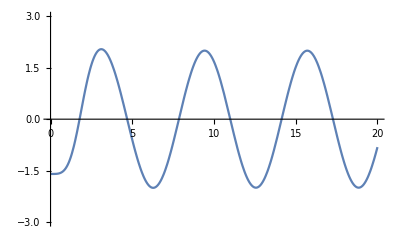

```mathematica
Plot[charEqz,{z,0,20},PlotRange->{-3,3}]
```

```mathematica
roots=FindRoot[charEqz,{z,{1.5,4.5,7.5,10.8,14}}][[1]]
```

z→{1.77596,4.6883,7.85352,10.9951,14.137}

```mathematica
βRule=β->z/L/.roots
```

β→{1.77596/L,4.6883/L,7.85352/L,10.9951/L,14.137/L}

```mathematica
ω=z^2 Sqrt[m/EI]/.roots
```

{3.15404 √(m/EI),21.9802 √(m/EI),61.6778 √(m/EI),120.892 √(m/EI),199.854 √(m/EI)}

Now our modes have the form:

```mathematica
Φ[x_]=sol/.C4Rule/.C3Rule/.C2Rule//Simplify
```

(C[1] (-Cos[x β] Sin[L β]+Cos[L β] Sin[x β]-Cos[x β] Sinh[L β]+Cosh[x β] (Sin[L β]+Sinh[L β])+Cosh[L β] (Sin[x β]-Sinh[x β])-Cos[L β] Sinh[x β]))/(Cos[L β]+Cosh[L β])

If we plug in the characteristic values, we get all the modes we solved for:

```mathematica
modes=Φ[x]/.βRule
```

{0.352869 C[1] (-3.84734 Cos[(1.77596 x)/L]+3.84734 Cosh[(1.77596 x)/L]-0.203729 Sin[(1.77596 x)/L]+3.03764 (Sin[(1.77596 x)/L]-Sinh[(1.77596 x)/L])+0.203729 Sinh[(1.77596 x)/L]),0.0184112 C[1] (-53.33 Cos[(4.6883 x)/L]+53.33 Cosh[(4.6883 x)/L]-0.0240836 Sin[(4.6883 x)/L]+54.3389 (Sin[(4.6883 x)/L]-Sinh[(4.6883 x)/L])+0.0240836 Sinh[(4.6883 x)/L]),0.000776764 C[1] (-1288.39 Cos[(7.85352 x)/L]+1288.39 Cosh[(7.85352 x)/L]+0.000461341 Sin[(7.85352 x)/L]+1287.39 (Sin[(7.85352 x)/L]-Sinh[(7.85352 x)/L])-0.000461341 Sinh[(7.85352 x)/L]),0.0000335678 C[1] (-29789.4 Cos[(10.9951 x)/L]+29789.4 Cosh[(10.9951 x)/L]-0.000484742 Sin[(10.9951 x)/L]+29790.4 (Sin[(10.9951 x)/L]-Sinh[(10.9951 x)/L])+0.000484742 Sinh[(10.9951 x)/L]),1.4502×10^-6 C[1] (-689561. Cos[(14.137 x)/L]+689561. Cosh[(14.137 x)/L]+0.00021087 Sin[(14.137 x)/L]+689560. (Sin[(14.137 x)/L]-Sinh[(14.137 x)/L])-0.00021087 Sinh[(14.137 x)/L])}

We can normalize them using the norm as:

```mathematica
mags=Chop[Integrate[modes^2,{x,0,L}],10^-6]^(-1/2)
```

{0.801196/(√(L C[1]^2)),1.02035/(√(L C[1]^2)),0.99946/(√(L C[1]^2)),1.0001/(√(L C[1]^2)),1.00002/(√(L C[1]^2))}

```mathematica
NModes=Simplify[Thread[modes mags],C[1]>0]
```

{(-1.08771 Cos[(1.77596 x)/L]+1.08771 Cosh[(1.77596 x)/L]+0.801196 Sin[(1.77596 x)/L]-0.801196 Sinh[(1.77596 x)/L])/(√L),(-1.00185 Cos[(4.6883 x)/L]+1.00185 Cosh[(4.6883 x)/L]+1.02035 Sin[(4.6883 x)/L]-1.02035 Sinh[(4.6883 x)/L])/(√L),(-1.00024 Cos[(7.85352 x)/L]+1.00024 Cosh[(7.85352 x)/L]+0.99946 Sin[(7.85352 x)/L]-0.99946 Sinh[(7.85352 x)/L])/(√L),(-1.00006 Cos[(10.9951 x)/L]+1.00006 Cosh[(10.9951 x)/L]+1.0001 Sin[(10.9951 x)/L]-1.0001 Sinh[(10.9951 x)/L])/(√L),(-1.00002 Cos[(14.137 x)/L]+1.00002 Cosh[(14.137 x)/L]+1.00002 Sin[(14.137 x)/L]-1.00002 Sinh[(14.137 x)/L])/(√L)}

Now, we can plot all of them:

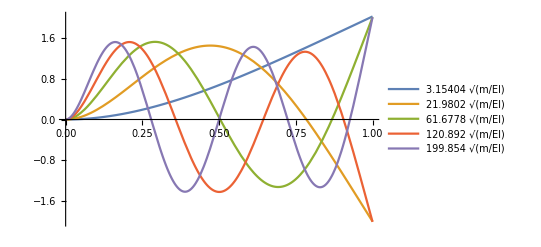

```mathematica
Plot[Evaluate[NModes/.L->1],{x,0,1},PlotLegends-> ω]
```